## Craft 1

### Import data

```mathematica
SetDirectory@FileNameJoin[{NotebookDirectory[],"data"}]
```

/Users/jiezhu/Documents/Wolfram Mathematica/Code for work/LV Cross Section/EBL/data

```mathematica
Last/@FileNameSplit/@FileNames[All,FileNameJoin[{NotebookDirectory[],"data"}]]
```

{CUBA_UVB.dat,ebl_dominguez11.out,ebl_dominguez.dat,eblerr_saldana21_comoving.txt,eblflux_fiducial.dat,eblflux_fixed.dat,ebl_franceschini.dat,ebl_lower_uncertainties_dominguez11.out,ebl_modelC_Finke.txt,ebl_nuFnu_tanja.dat,EBL_nuInu_model_A_Finke2022.dat,EBL_proper_baseline.dat,EBL_proper_low_pop3.dat,EBL_proper_up_pop3.dat,ebl_saldana21_comoving.txt,ebl_upper_uncertainties_dominguez11.out,EBL_z_0_baseline.dat,EBL_z_0_low_pop3.dat,EBL_z_0_up_pop3.dat,nuInu_kneiske.dat,opdep_fiducial.dat,opdep_fixed.dat,tau_dominguez10.dat,tau_dominguez11_cta.out,tau_ebl_cmb_kneiske_bestfit.dat,tau_ebl_cmb_kneiske.dat,tau_fran08.dat,tau_fran17.dat,tau_gg_baseline.dat,tau_gg_low_pop3.dat,tau_gg_up_pop3.dat,tau_high_saldana-lopez21.out,tau_lower_dominguez11_cta.out,tau_low_saldana-lopez21.out,tau_model_A_Finke2022.dat,tau_modelC_Finke.txt,tau_saldana-lopez21.out,tau_upper_dominguez11_cta.out}

```mathematica
data=Import["EBL_nuInu_model_A_Finke2022.dat","Table"]//DeleteCases[#,{"#",___}]&;
```

```mathematica
zs=data[[1,2;;-1]];
```

```mathematica
λs=data[[2;;-1,1]];
```

```mathematica
lil=data[[2;;-1,2;;-1]];
```

```mathematica
Dimensions/@{zs,λs,lil}
```

{{351},{199},{199,351}}

```mathematica
Flatten[#,1]&@Outer[List,λs,zs]//Short[#,10]&
```

{{0.0345514800000000025,0.},{0.0345514800000000025,0.0200000000000000004},{0.0345514800000000025,0.0400000000000000008},{0.0345514800000000025,0.0599999999999999978},«69841»,{1243.10000000000014,6.94000000000000039},{1243.10000000000014,6.95999999999999996},{1243.10000000000014,6.98000000000000043},{1243.10000000000014,7.}}

```mathematica
MapThread[List,{Flatten[#,1]&@Outer[List,λs,zs],Flatten[#,1]&@lil}]//Short[#,10]&
```

{{{0.0345514800000000025,0.},8.66074900000000013×10^-52},{{0.0345514800000000025,0.0200000000000000004},8.48123000000000071×10^-52},{{0.0345514800000000025,0.0400000000000000008},8.3068080000000003×10^-52},«69844»,{{1243.10000000000014,6.98000000000000043},3.92396699999999976×10^-6},{{1243.10000000000014,7.},3.89159099999999969×10^-6}}

```mathematica
Flatten[#,1]&@MapThread[List,{Outer[List,λs,zs],lil},2]//Short[#,10]&
```

{{{0.0345514800000000025,0.},8.66074900000000013×10^-52},{{0.0345514800000000025,0.0200000000000000004},8.48123000000000071×10^-52},{{0.0345514800000000025,0.0400000000000000008},8.3068080000000003×10^-52},«69844»,{{1243.10000000000014,6.98000000000000043},3.92396699999999976×10^-6},{{1243.10000000000014,7.},3.89159099999999969×10^-6}}

```mathematica
func=Interpolation[Flatten[#,1]&@MapThread[List,{Outer[List,λs,zs],lil},2]]
```

InterpolatingFunction[{{0.0345515, 1243.1}, {0., 7.}}, <>]

```mathematica
Plot3D[func[l,z],{l,0.1,1000},{z,0,3.9},PlotRange->All]
```

-Graphics3D-

Parameters:

        z:  source redshift, m-dimensional

        lmu:  wavelenghts in micrometer, n-dimensional

        Return:  corresponding (nu I nu) values [nW / m^2 / sr]

```mathematica
Intensity=func;
```

### Units in SI

```mathematica
c=299792458.;(*m/s*)
h=6.62607015*^-34;(*kg m^2/s*)

eV=1.602176634*^-19;(*eV to J, J*)
keV=1*^3 eV;
MeV=1*^3 keV;
GeV=1*^3 MeV;
TeV=1*^3 GeV;
PeV=1*^3 TeV;
Mpl=1.220890*^19 GeV;

me=0.5110 MeV(*mass of electron*);

um=1*^-6;(*micro meter, m*)
km=1*^3;
Mpc=3.08567758*^22;(*Mpc to meter,m*)

(*Cosmology parameters*)
Om=0.315;
Ol=0.685;
H0=70*km/1/Mpc;(*km/s/Mpc to Hz*)

σT=6.6524587321*^-29;(*Thomson cross-section, m^2*)
```

```mathematica
H0
```

2.26855×10^-18

```mathematica
h c/eV/um
```

1.23984

```mathematica
eVToum[e_]:=h c/eV/um/e
```

```mathematica
eVToum[1]
```

1.23984

```mathematica
umToeV[l_]:=h c/eV/um/l
```

```mathematica
λs-eVToum/@umToeV/@λs//Abs//Total
```

0

```mathematica
Density[e_,z_]:=Module[{l,intensity,temp},
l=eVToum[e];
intensity=Intensity[l,z];
temp=4π/c/(e eV)^2*intensity*1*^-9;(*1/J/m^3*)
temp* eV*1*^-6(*1/eV/cm^3*)
]
```

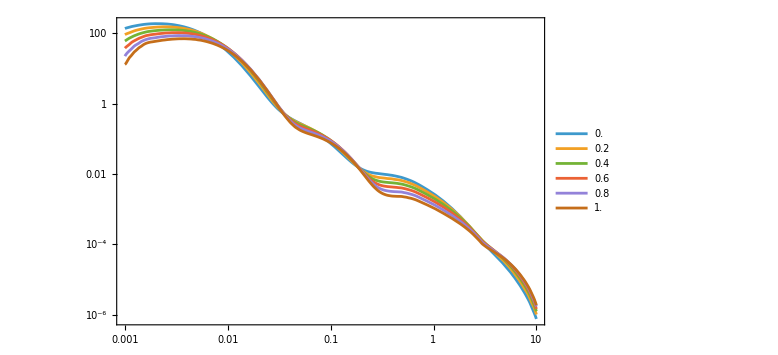

```mathematica
LogLogPlot[Table[Density[x,z],{z,0,1,0.2}]//Evaluate,{x,1*^-3,10},Frame->True,(*PlotLegends->Placed[Range[0,1,0.2], {Right,Top}],*)PlotLegends->Placed[LineLegend[Range[0,1,0.2],(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Right,Top}],ImageSize->Large]
```

```mathematica
es=umToeV/@λs;
```

```mathematica
data2=Flatten[#,1]&@Outer[{{#1,#2},Density[#1,#2]}&,umToeV/@λs,zs];
```

```mathematica
func2=Interpolation[data2]
```

InterpolatingFunction[{{0.000997379, 35.8839}, {0., 7.}}, <>]

```mathematica
Plot3D[{func2[x,y]-Density[x,y]}/Density[x,y],{x,1*^-3,10},{y,0,2},PlotRange->All]
```

-Graphics3D-

```mathematica
Outer[Function[{x,y},func2[x,y]-Density[x,y]],es,zs]//Abs//Total//Total//AbsoluteTiming
```

{0.80524,0.}

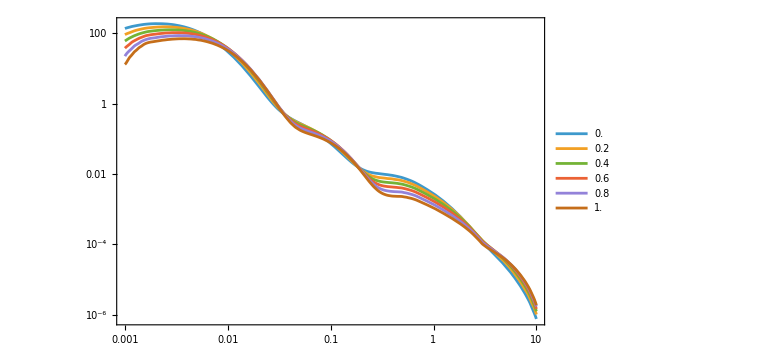

```mathematica
LogLogPlot[Table[func2[x,z],{z,0,1,0.2}]//Evaluate,{x,1*^-3,10},Frame->True,(*PlotLegends->Placed[Range[0,1,0.2], {Right,Top}],*)PlotLegends->Placed[LineLegend[Range[0,1,0.2],(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Right,Top}],ImageSize->Large]
```

### integral

```mathematica
dldz[z_]:=1/H0 1/(1+z)√(Ol+Om(1+z)^3)(*1/s*)
```

```mathematica
dnde[e_(*eV*),z_]:=func2[e,z]/eV/1*^-6(*1/J/m^3*)
```

-Graphics-

```mathematica
σ[β_]:=3/16σT(1-β^2)(2β(β^2-2)+(3-β^4)Log[(1+β)/(1-β)])
```

-Graphics-

```mathematica
β[ein_,z_,ϵ_(*eV*),μ_]:=√(1-2 me^2/(ein ϵ eV)1/(1-μ)(1/(1+z))^2)
```

-Graphics-

```mathematica
dldz[z]dnde[ϵ,z](1-μ)/2 σ[β[ein,z,ϵ,μ]]
```

1/(ein (1+z)^3 ϵ)1.43575×10^6 √(0.685+0.315 (1+z)^3) (2 (-1-(8.36724×10^-8)/(ein (1+z)^2 ϵ (1-μ))) √(1-(8.36724×10^-8)/(ein (1+z)^2 ϵ (1-μ)))+(3-(1-(8.36724×10^-8)/(ein (1+z)^2 ϵ (1-μ)))^2) Log[(1+√(1-(8.36724×10^-8)/(ein (1+z)^2 ϵ (1-μ))))/(1-√(1-(8.36724×10^-8)/(ein (1+z)^2 ϵ (1-μ))))]) InterpolatingFunction[{{0.000997379, 35.8839}, {0., 7.}}, <>][ϵ,z]

```mathematica
β[ein,z,ϵ,μ]/.{z->0.1,ein->10TeV,μ->0.1,ϵ->0.2}
```

0.871906

```mathematica
β[10TeV,0.1,1,0]
```

0.978182

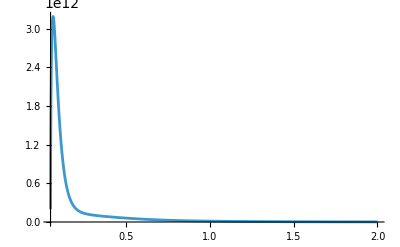

```mathematica
Plot[/.{z->0.1,ein->10TeV,μ->0.1},{ϵ,1*^-3,2},PlotRange->All]
```

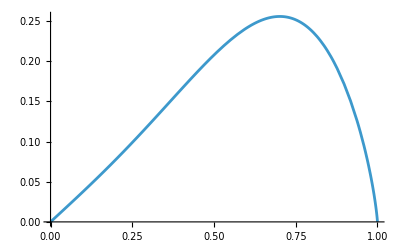

```mathematica
Plot[σ[β]/σT,{β,0,1}]
```

## Craft 2

```mathematica
σ[β_]:=3/16σT(1-β^2)(2β(β^2-2)+(3-β^4)Log[(1+β)/(1-β)])/.σT->1
```

```mathematica
With[{A=0.001},NIntegrate[(1-μ)/2 σ[√(1-2 A/(1-μ))],{μ,-1,1-2A},Exclusions->{-1,1}]]
```

0.00474001

```mathematica
P[x_]:=Log[2]^2-π^2/6+2 PolyLog[2,(1-x)/2]-(x+x^3)/(1-x^2)+(Log[1+x]-2Log[2])Log[1-x]+1/2(Log[1-x]^2-Log[1+x]^2)+(1+x^4)/(2(1-x^2))Log[(1+x)/(1-x)]
```

```mathematica
With[{A=0.001},P[√(1-A)]A^2]
```

0.00632001

```mathematica
/
```

0.75

```mathematica
√(1-(4 me^2)/(2 ω ϵ (1-Cos[θ])-ξ ω^(n+2)))
```

```mathematica
Solve[√(1-(4 me^2)/(2 ω ϵ (1-Cos[θ])-ξ ω^(n+2)))==0,ϵ]
```

{{ϵ→(-4 me^2-ξ ω^(2+n))/(2 ω (-1+Cos[θ]))}}

```mathematica
$UserBaseDirectory//SystemOpen
```

## Craft 3: with LV

```mathematica
σ[β_]:=3/16(1-β^2)(2β(β^2-2)+(3-β^4)Log[(1+β)/(1-β)])
```

```mathematica
(E0^2-P0^2)+2E0 ϵb-2P0 ϵb Cos[θ]/.P0->√(E0^2-ξ ϵ[E0])//Series[#,{ξ,0,1},Assumptions->E0>0]&//Simplify
```

-2 (E0 ϵb (-1+Cos[θ]))+((E0+ϵb Cos[θ]) ϵ[E0] ξ)/E0+O[ξ]^2

A=m_e^2/(ϵ_b E),  B=(ξ ϵ[E])/(2 ϵ_b E)  ,  E^2-P^2=ξ ϵ[E]

```mathematica
rule1={A->me^2/(ϵb E0), B->ξ ϵ[E0]/(2 ϵb E0)};
```

```mathematica
rule2={ϵ->Function[-#^(n+2)],ξ->1/Elv^n};
```

```mathematica
β->√(1-(2A)/(1-Cos[θ]+B))/.rule1/.rule2
```

β→√(1-(2 me^2)/(E0 ϵb (1-(E0^(1+n) Elv^-n)/(2 ϵb)-Cos[θ])))

```mathematica
Solve[β==√(1-(2A)/(1-Cos[θ]+B))/.Cos[θ]->μ,μ]//Simplify
```

Solve::nongen: 可能存在使某些解或所有解都无效的参数值.

{{μ→1+B+(2 A)/(-1+β^2)}}

```mathematica
Solve[0==√(1-(2A)/(1-Cos[θ]+B))/.Cos[θ]->μ,μ]
```

{{μ→1-2 A+B}}

```mathematica
rule1/.rule2/.{E0->10TeV,Elv->0.03 Mpl,ϵb->1eV,n->1}
```

{A→0.0261121,B→-0.136512}

0.811263

√(1-0.0522242/(0.863488-μ))

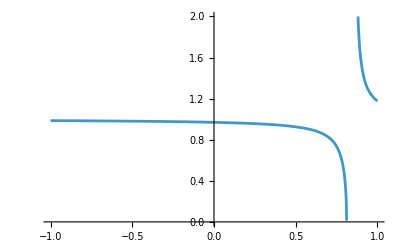

```mathematica
1-2 A+B/.rule1/.rule2/.{E0->10TeV,Elv->0.03Mpl,ϵb->1eV,n->1}
√(1-(2A)/(1-μ+B))/.rule1/.rule2/.{E0->10TeV,Elv->0.03Mpl,ϵb->1eV,n->1}
Plot[%,{μ,-1,1},PlotRange->{0,2}]
```

√(1-0.0522242/(1-μ))

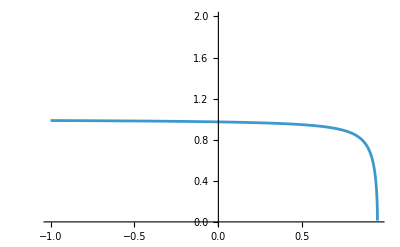

```mathematica
√(1-(2A)/(1-μ))/.rule1/.rule2/.{E0->10TeV,Elv->0.03Mpl,ϵb->1eV,n->1}
Plot[%,{μ,-1,1},PlotRange->{0,2}]
```

```mathematica
Manipulate[Plot[{(1-Cos[θ])/2 σ[√(1-(2A)/(1-Cos[θ]))]Sin[θ],(1-Cos[θ])/2 σ[√(1-(2A)/(1-Cos[θ]+B))]Sin[θ]}/.rule1/.rule2/.{E0->10TeV,Elv->x Mpl,ϵb->0.1eV,n->1}//Evaluate,{θ,0,π}],{{x,0.03},0.01,2}]
```

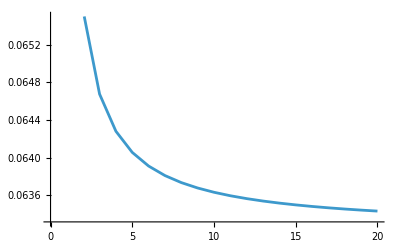

```mathematica
Table[Hold[NIntegrate[(1-μ)/2 σ[√(1-(2A)/(1-μ+B))],{μ,-1,1-2A+B},Exclusions->{-1,1}]]/.rule1/.rule2/.{E0->10TeV,Elv->x Mpl,ϵb->1eV,n->1}//ReleaseHold,{x,0.03,1,0.05}]//ListLinePlot
```

```mathematica
Assuming[β>0,(1-μ)/2 σgg[√(1-(2A)/(1-μ+B))]D[1+B+(2 A)/(-1+β^2),β]/.μ->1+B+(2 A)/(-1+β^2)//Simplify]
```

(2 A β (2 A+B (-1+β^2)) σgg[β])/((-1+β^2)^3)

-1<μ<1-2 A+B

```mathematica
√(1-(2A)/(1-μ+B))/.{{μ->-1},{μ->1-2 A+B}}
```

{√(1-(2 A)/(2+B)),0}

```mathematica
IntegrateChangeVariables[Inactive[Integrate][(1-μ)/2 σgg[√(1-(2A)/(1-μ+B))],{μ,-1,1-2 A+B}],β,β==√(1-(2A)/(1-μ+B)),Assumptions->{β>0,A>0,-1<B<0}]
```

ConditionalExpression[(2 A β (2 A+B (-1+β^2)) σgg[β])/((-1+β^2)^3)β0√((2-2 A+B)/(2+B)), (A<1&&2 A<2+B)||2 A≤1]

```mathematica
(2 A β (2 A+B (-1+β^2)) σgg[β])/((-1+β^2)^3)/.σgg->σ
```

(3 A β (1-β^2) (2 A+B (-1+β^2)) (2 β (-2+β^2)+(3-β^4) Log[(1+β)/(1-β)]))/(8 (-1+β^2)^3)

```mathematica
Inactive[Integrate][(3 A β (1-β^2) (2 A+B (-1+β^2)) (2 β (-2+β^2)+(3-β^4) Log[(1+β)/(1-β)]))/(8 (-1+β^2)^3),{β,0,√(1-(2 A)/(2+B))}]
```

(3 A β (1-β^2) (2 A+B (-1+β^2)) (2 β (-2+β^2)+(3-β^4) Log[(1+β)/(1-β)]))/(8 (-1+β^2)^3)β0√(1-(2 A)/(2+B))

```mathematica
Integrate[-(3 A β (1-β^2) (2 A+B (-1+β^2)) (2 β (-2+β^2)+(3-β^4) Log[(1+β)/(1-β)]))/(8 (-1+β^2)^3),{β,0,βmax},Assumptions->{0<βmax<1},GenerateConditions->False]
```

-1/(32 (-1+βmax^2))3 A (-8 A βmax-14 B βmax-8 A βmax^3+16 B βmax^3-2 B βmax^5+4 A Log[1-βmax]-7 B Log[1-βmax]-4 A βmax^2 Log[1-βmax]+7 B βmax^2 Log[1-βmax]-4 A Log[4] Log[1-βmax]+4 A βmax^2 Log[4] Log[1-βmax]-2 B βmax^2 Log[4] Log[1-βmax]+B Log[16] Log[1-βmax]-4 A Log[1-βmax]^2+2 B Log[1-βmax]^2+4 A βmax^2 Log[1-βmax]^2-2 B βmax^2 Log[1-βmax]^2-4 A Log[1+βmax]+7 B Log[1+βmax]+4 A βmax^2 Log[1+βmax]-7 B βmax^2 Log[1+βmax]+4 A Log[4] Log[1+βmax]-2 B Log[4] Log[1+βmax]-4 A βmax^2 Log[4] Log[1+βmax]+B βmax^2 Log[16] Log[1+βmax]+4 A Log[1+βmax]^2-2 B Log[1+βmax]^2-4 A βmax^2 Log[1+βmax]^2+2 B βmax^2 Log[1+βmax]^2+8 A Log[(1+βmax)/(1-βmax)]-4 A βmax^2 Log[(1+βmax)/(1-βmax)]-2 B βmax^2 Log[(1+βmax)/(1-βmax)]+4 A βmax^4 Log[(1+βmax)/(1-βmax)]+B βmax^4 Log[(1+βmax)/(1-βmax)]+B βmax^6 Log[(1+βmax)/(1-βmax)]-8 A Log[1-βmax] Log[(1+βmax)/(1-βmax)]+4 B Log[1-βmax] Log[(1+βmax)/(1-βmax)]+8 A βmax^2 Log[1-βmax] Log[(1+βmax)/(1-βmax)]-4 B βmax^2 Log[1-βmax] Log[(1+βmax)/(1-βmax)]-8 A Log[1+βmax] Log[(1+βmax)/(1-βmax)]+4 B Log[1+βmax] Log[(1+βmax)/(1-βmax)]+8 A βmax^2 Log[1+βmax] Log[(1+βmax)/(1-βmax)]-4 B βmax^2 Log[1+βmax] Log[(1+βmax)/(1-βmax)]-4 (2 A-B) (-1+βmax^2) PolyLog[2,(1-βmax)/2]+4 (2 A-B) (-1+βmax^2) PolyLog[2,(1+βmax)/2])

```mathematica
Collect[,{B,A},TrigToExp@FullSimplify[#,Assumptions->{0<βmax<1}]&]
```

-3/16 A B (7 βmax-βmax^3+Log[1-βmax]^2-Log[1+βmax]^2+1/2 (-7+2 βmax^2+βmax^4+Log[16]) (-Log[1-βmax]+Log[1+βmax])+2 PolyLog[2,(1-βmax)/2]-2 PolyLog[2,(1+βmax)/2])+1/(8 (-1+βmax^2))3 A^2 (2 (βmax+βmax^3)-Log[1-βmax]^2+Log[1+βmax]^2+(1+βmax^4+Log[4]+βmax^2 Log[1/4 (1-βmax^2)]) Log[-1+2/(1+βmax)]+2 (-1+βmax^2) PolyLog[2,(1-βmax)/2]-2 (-1+βmax^2) PolyLog[2,(1+βmax)/2])

```mathematica
{term1,term2}=List@@//Reverse;
```

```mathematica
With[{A=0.1,B=-0.1},NIntegrate[(1-μ)/2 σ[√(1-(2A)/(1-μ+B))]/σT,{μ,-1,1-2A+B},Exclusions->{-1,1}]]
```

0.154662

```mathematica
term1+term2/.βmax->√(1-(2 A)/(2+B))/.{A->0.1,B->-0.1}
```

0.154662

```mathematica
term1/.βmax->√(1-(2 A)/(2+B))/.{A->0.1,B->0}
```

0.150741

```mathematica
3/4 A^2P[x]/.x->√(1-A)/.{A->0.1,B->0}
```

0.150741

```mathematica
term1-3/4 A^2P[x]/.x->βmax//FullSimplify[#,Assumptions->{0<βmax<1}]&
```

1/8 A^2 (π^2-6 Log[2]^2-6 Log[1-βmax] Log[1+βmax]+Log[64] Log[1-βmax^2]-6 PolyLog[2,(1-βmax)/2]-6 PolyLog[2,(1+βmax)/2])

```mathematica
simp=Solve[==0,PolyLog[2,(1+βmax)/2]][[1,1]]
```

PolyLog[2,(1+βmax)/2]→1/6 (π^2-6 Log[2]^2-6 Log[1-βmax] Log[1+βmax]+Log[64] Log[1-βmax^2]-6 PolyLog[2,(1-βmax)/2])

```mathematica
term1//FullSimplify[#,Assumptions->{0<βmax<1}]&
```

1/(8 (-1+βmax^2))3 A^2 (2 (βmax+βmax^3)-Log[1-βmax]^2+Log[1+βmax]^2+(1+βmax^4+Log[4]+βmax^2 Log[1/4 (1-βmax^2)]) Log[-1+2/(1+βmax)]+2 (-1+βmax^2) PolyLog[2,(1-βmax)/2]-2 (-1+βmax^2) PolyLog[2,(1+βmax)/2])

```mathematica
term2/.simp//FullSimplify[#,Assumptions->{0<βmax<1}]&
```

1/16 A B (π^2-21 βmax+3 βmax^3-6 Log[2]^2-3 ArcTanh[βmax] (-7+2 βmax^2+βmax^4+Log[16])-3 Log[1-βmax]^2-6 Log[1-βmax] Log[1+βmax]+3 Log[1+βmax]^2+Log[64] Log[1-βmax^2]-12 PolyLog[2,(1-βmax)/2])

```mathematica
term1+term2
```

-3/16 A B (7 βmax-βmax^3+Log[1-βmax]^2-Log[1+βmax]^2+1/2 (-7+2 βmax^2+βmax^4+Log[16]) (-Log[1-βmax]+Log[1+βmax])+2 PolyLog[2,(1-βmax)/2]-2 PolyLog[2,(1+βmax)/2])+1/(8 (-1+βmax^2))3 A^2 (2 (βmax+βmax^3)-Log[1-βmax]^2+Log[1+βmax]^2+(1+βmax^4+Log[4]+βmax^2 Log[1/4 (1-βmax^2)]) Log[-1+2/(1+βmax)]+2 (-1+βmax^2) PolyLog[2,(1-βmax)/2]-2 (-1+βmax^2) PolyLog[2,(1+βmax)/2])

```mathematica
{term1,term1+term2}/.βmax->√(1-(2 A)/(2+B))/.rule1/.rule2/.{E0->10TeV,Elv->0.03Mpl,ϵb->1eV,n->1}
```

{0.0577549,0.0691996}

```mathematica
rule1
```

{A→(6.7029×10^-27)/(E0 ϵb),B→(ξ ϵ[E0])/(2 E0 ϵb)}

```mathematica
rule2
```

{ϵ→(-#1^(n+2)&),ξ→Elv^-n}

```mathematica
√(1-(2 A)/(2+B))/.rule1/.rule2/.{E0->100TeV,ϵb->0.001eV,n->1,Elv->x Mpl}
```

√(1-5.22242/(2-409.537/x))

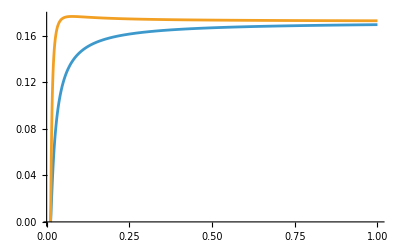

```mathematica
Plot[{term1,term1+term2}/.βmax->√(1-(2 A)/(2+B))/.rule1/.rule2/.{E0->10TeV,ϵb->0.2eV,n->1,Elv->x Mpl}//Evaluate,{x,0.01,1},PlotRange->All]
```

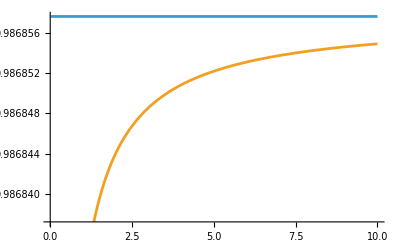

```mathematica
Plot[{√(1-(2 A)/2),√(1-(2 A)/(2+B))}/.rule1/.rule2/.{E0->10TeV,ϵb->1eV,n->1,Elv->x Mpl}//Evaluate,{x,0.01,10}]
```

```mathematica
Hold[NIntegrate[(1-μ)/2 σ[√(1-(2A)/(1-μ+B))],{μ,-1,1-2A+B},Exclusions->{-1,1}]]/.rule1/.rule2/.{E0->10TeV,Elv->0.03 Mpl,ϵb->0.2eV,n->1}//ReleaseHold
```

0.164455

```mathematica
Hold[NIntegrate[(1-Cos[θ])/2 σ[√(1-(2A)/(1-Cos[θ]+B))]Sin[θ]Boole[1-(2A)/(1-Cos[θ]+B)>0]Boole[1-Cos[θ]+B>0],{θ,0,π},Exclusions->{-1,1}]]/.rule1/.rule2/.{E0->10TeV,Elv->0.03 Mpl,ϵb->0.2eV,n->1}//ReleaseHold
```

NIntegrate::ncvb: 在接近 {θ} = {1.51552} 处的 θ 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.164455 和 1.84461×10^-6.

0.164455

```mathematica
Cos[1.5155241929272922]
```

0.055244

```mathematica
1-2A+B/.rule1/.rule2/.{E0->10TeV,Elv->0.03 Mpl,ϵb->0.2eV,n->1}
```

0.0563168

```mathematica
{term1,term1+term2}/.βmax->√(1-(2 A)/(2+B))/.rule1/.rule2/.{E0->10TeV,ϵb->0.2eV,n->1,Elv->0.03 Mpl}
```

{0.0874492,0.164455}

```mathematica
Manipulate[Plot[{(1-μ)/2 σ[√(1-(2A)/(1-μ))],(1-μ)/2 σ[√(1-(2A)/(1-μ+B))]}/.rule1/.rule2/.{E0->10TeV,Elv->x Mpl,ϵb->0.2eV,n->1}//Evaluate,{μ,-1,1}],{{x,0.03},0.01,2}]
```

```mathematica
{1+B-2A,1-2A}/.rule1/.rule2/.{E0->10TeV,Elv->0.03 Mpl,ϵb->0.2eV,n->1}
```

{0.0563168,0.738879}

```mathematica
Plot[σ[β],{β,0,1}]
```

```mathematica
NMaximize[σ[β],{β,0,1}]
```

{0.25564,{β→0.701317}}

```mathematica
FindRoot[σ[β]==0.2556395645631702/E,{β,0.9}]
```

{β→0.959117}

```mathematica
√(1-(me^2/(2 ϵ E0))/(1+1))==0.9591169716976626/.{ϵ->0.1eV}
```

√(1-(1.0459×10^-7)/E0)==0.959117

```mathematica
Solve[,E0][[1,1,2]]/TeV
```

8.15039

```mathematica
√(1-(me^2/(2 ϵ E0))/((1-μ)-E0^3/Elv/(2 ϵ E0)))/.{ϵ->0.1eV,E0->8.15 TeV,μ->-1,ϵ->0.1eV}
```

√(1-0.160197/(2-(5.32103×10^7)/Elv))

```mathematica
Solve[==0.7,Elv][[1,1,2]]/GeV
```

1.96996×10^17

```mathematica
{√(1-(4 me^2)/(2 ϵ E0 (1-μ))),√(1-(me^2/(2 ϵ E0))/((1-μ)-E0^3/Elv/(2 ϵ E0)))}/.{E0->3TeV,ϵ->0.1eV,Elv->0.00003Mpl}
```

{√(1-1.74081/(1-μ)),√(1-0.435202/(-121.861-μ))}

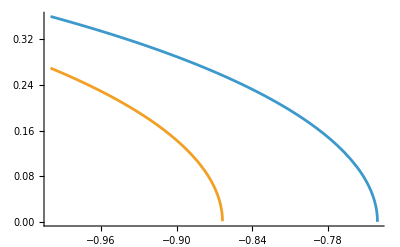

```mathematica
Plot[{√(1-(4 me^2)/(2 ϵ E0 (1-μ))),√(1-(4 me^2)/(2 ϵ E0 (1-μ)-E0^3/Elv))}/.{E0->3TeV,ϵ->0.1eV,Elv->0.03Mpl}//Evaluate,{μ,-1,1-2me^2/(ϵ E0)/.{E0->3TeV,ϵ->0.1eV}}]
```

```mathematica
me^2/(0.1eV)/TeV
```

2.61121

```mathematica
{σ[0.96],σ[0.89]}
```

{0.0926016,0.179204}

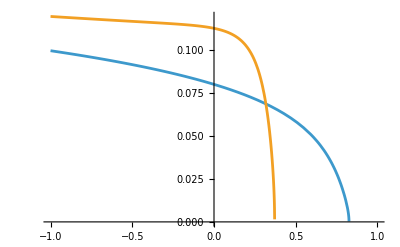

```mathematica
Plot[{(1-μ)/2 σ[√(1-(4 me^2)/(2 ϵ E0 (1-μ)))],(1-μ)/2 σ[√(1-(4 me^2)/(2 ϵ E0 (1-μ)-E0^3/Elv))]}/.{E0->10TeV,ϵ->0.3eV,Elv->0.03Mpl}//Evaluate,{μ,-1,1}]
```

```mathematica
1/(32 π Subscript[m, e]^2)("e")^4 (Elv^-n (1-β^2)^(1-n/2) Subscript[m, e]^n (β (β^2-2) (n-1)-1/2 (log(β+1)-log(1-β)) (2 β^2+β^4 (n-1)-3 n+1))-(β^2-1) ((β^4-3) log(1-β)-(β^4-3) log(β+1)+2 β (β^2-2)))//InputForm
```

("e"^4*(-((-1 + β^2)*(2*β*(-2 + β^2) + (-3 + β^4)*Log[1 - β] - 
      (-3 + β^4)*Log[1 + β])) + 
   ((1 - β^2)^(1 - n/2)*((-1 + n)*β*(-2 + β^2) - 
      ((1 - 3*n + 2*β^2 + (-1 + n)*β^4)*(-Log[1 - β] + Log[1 + β]))/2)*
     Subscript[m, e]^n)/Elv^n))/(32*Pi*Subscript[m, e]^2)

```mathematica
("e"^4*(-((-1 + β^2)*(2*β*(-2 + β^2) + (-3 + β^4)*Log[1 - β] - 
      (-3 + β^4)*Log[1 + β])) + 
   ((1 - β^2)^(1 - n/2)*((-1 + n)*β*(-2 + β^2) - 
      ((1 - 3*n + 2*β^2 + (-1 + n)*β^4)*(-Log[1 - β] + Log[1 + β]))/2)*
     Subscript[m, e]^n)/Elv^n))/(32*Pi*Subscript[m, e]^2)
```

1/(32 π m_e^2)e^4 (-((-1+β^2) (2 β (-2+β^2)+(-3+β^4) Log[1-β]-(-3+β^4) Log[1+β]))+Elv^-n (1-β^2)^(1-n/2) ((-1+n) β (-2+β^2)-1/2 (1-3 n+2 β^2+(-1+n) β^4) (-Log[1-β]+Log[1+β])) m_e^n)

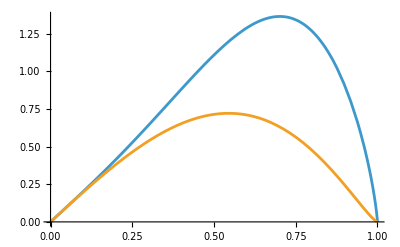

```mathematica
Plot[{-((-1+β^2) (2 β (-2+β^2)+(-3+β^4) Log[1-β]-(-3+β^4) Log[1+β])),(1-β^2)^(1-n/2) ((-1+n) β (-2+β^2)-1/2 (1-3 n+2 β^2+(-1+n) β^4) (-Log[1-β]+Log[1+β]))}/.n->1//Evaluate,{β,0,1},PlotRange->All]
```

```mathematica
(1-β^2)^(1-n/2) ((-1+n) β (-2+β^2)-1/2 (1-3 n+2 β^2+(-1+n) β^4) (-Log[1-β]+Log[1+β]))/.n->2
```

β (-2+β^2)-1/2 (-5+2 β^2+β^4) (-Log[1-β]+Log[1+β])

```mathematica
$UserBaseDirectory//SystemOpen
```

## Craft 4: LV only causes threshold shift of EBL:

### Import data

```mathematica
SetDirectory@FileNameJoin[{NotebookDirectory[],"data"}]
```

/Users/jiezhu/Documents/Wolfram Mathematica/Code for work/LV Cross Section/EBL/data

```mathematica
data=Import["EBL_nuInu_model_A_Finke2022.dat","Table"]//DeleteCases[#,{"#",___}]&;
```

```mathematica
zs=data[[1,2;;-1]];
```

```mathematica
λs=data[[2;;-1,1]];
```

```mathematica
lil=data[[2;;-1,2;;-1]];
```

```mathematica
Dimensions/@{zs,λs,lil}
```

{{351},{199},{199,351}}

```mathematica
func=Interpolation[Flatten[#,1]&@MapThread[List,{Outer[List,λs,zs],lil},2]]
```

InterpolatingFunction[{{0.0345515, 1243.1}, {0., 7.}}, <>]

```mathematica
Plot3D[func[l,z],{l,0.1,1000},{z,0,3.9},PlotRange->All]
```

-Graphics3D-

func Parameters:

        z:  source redshift, m-dimensional

        lmu:  wavelenghts in micrometer, n-dimensional

        Return:  corresponding (nu I nu) values [nW / m^2 / sr]

### Units in SI

```mathematica
c=299792458.;(*m/s*)
h=6.62607015*^-34;(*kg m^2/s*)

eV=1.602176634*^-19;(*eV to J, J*)
keV=1*^3 eV;
MeV=1*^3 keV;
GeV=1*^3 MeV;
TeV=1*^3 GeV;
PeV=1*^3 TeV;
Mpl=1.220890*^19 GeV;

me=0.5110 MeV(*mass of electron*);

um=1*^-6;(*micro meter, m*)
cm=1*^-2;
km=1*^3;
Mpc=3.08567758*^22;(*Mpc to meter,m*)

(*Cosmology parameters*)
Om=0.315;
Ol=0.685;
H0=70*km/1/Mpc;(*km/s/Mpc to Hz*)

σT=6.6524587321*^-29;(*Thomson cross-section, m^2*)
```

```mathematica
Clear[Intensity];
(*Input: m, Output: W/m^2/sr*)
Intensity[l_,z_]=1*^-9func[l/um,z];
```

```mathematica
(*Input: J, Output: 1/J/m^3*)
Density[e_,z_]:=Module[{l,intensity,temp},
l=h c /e ;
intensity=Intensity[l,z];
temp=4π/c/e ^2*intensity(*1/J/m^3*)
]
```

```mathematica
LogLogPlot[Table[Density[x eV,z]* eV*cm^3(*1/eV/cm^3*),{z,0,1,0.2}]//Evaluate,{x,1*^-3,10},Frame->True,PlotLegends->Placed[LineLegend[Range[0,1,0.2],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Right,Top}],ImageSize->Large]
```

-Graphics-

```mathematica
data2=Flatten[#,1]&@Outer[{{#1,#2},Density[#1,#2]}&,h c /(λs*um),zs];
```

```mathematica
func2=Interpolation[data2]
```

-22            -18
InterpolatingFunction[{{1.59798 10   , 5.74924 10   }, {0., 7.}}, <>]

```mathematica
{emin,emax}=MinMax[h c /(λs*um)];
{emin,emax}/eV
```

{0.000997379,35.8839}

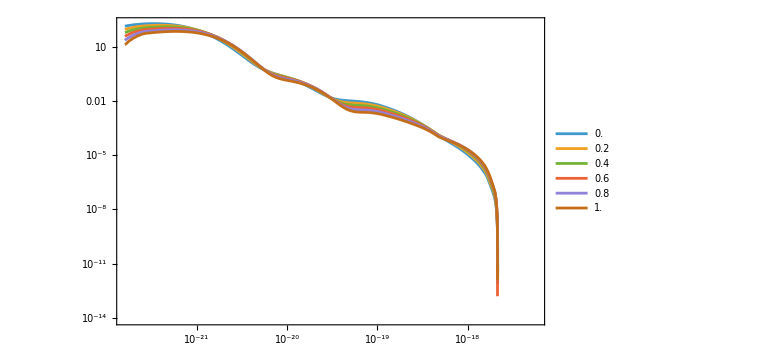

```mathematica
LogLogPlot[Table[func2[x,z]*eV*cm^3,{z,0,1,0.2}]//Evaluate,{x,emin,emax},Frame->True,(*PlotLegends->Placed[Range[0,1,0.2], {Right,Top}],*)PlotLegends->Placed[LineLegend[Range[0,1,0.2],(*LegendLabel->"label",*)LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Left,Bottom}],ImageSize->Large,
(*PlotRange->All,*)
PlotPoints->300]
```

### Functions

```mathematica
σ[β_]:=3/16σT(1-β^2)(2β(β^2-2)+(3-β^4)Log[(1+β)/(1-β)])
```

```mathematica
P[x_]:=Log[2]^2-π^2/6+2 PolyLog[2,(1-x)/2]-(x+x^3)/(1-x^2)+(Log[1+x]-2Log[2])Log[1-x]+1/2(Log[1-x]^2-Log[1+x]^2)+(1+x^4)/(2(1-x^2))Log[(1+x)/(1-x)]
```

```mathematica
σ[0.7]
```

1.70061×10^-29

```mathematica
dldz[z_]:=1/(1+z)1/(√(Ol+Om(1+z)^3))
```

```mathematica
τ[E0_,z0_]:=3/4(σT c)/H0 NIntegrate[dldz[z]func2[ϵ,z](me^2/(E0(1+z)ϵ))^2 P[√(1-me^2/(E0(1+z)ϵ))],{z,0,z0},{ϵ,Min[Max[emin,me^2/(E0 (1+z))],emax],emax}]//Quiet;
```

```mathematica
τ[E0_,z0_,elv_]:=3/4(σT c)/H0 NIntegrate[dldz[z]func2[ϵ,z](me^2/(E0(1+z)ϵ))^2 P[√(1-me^2/(E0(1+z)ϵ))],{z,0,z0},{ϵ,Min[Max[emin,me^2/(E0 (1+z))+(E0(1+z))^2/(4elv)],emax],emax}]//Quiet;
```

```mathematica
τ[10TeV,0.15]
```

4.53724

```mathematica
τ[1TeV,0.15]
```

1.13177

```mathematica
tab=ParallelMap[{#,Exp[-τ[#*TeV,0.15]]}&,PowerRange[10^-2,10^2,10.^(4/100)]];
```

```mathematica
tab2=ParallelMap[{#,Exp[-τ[#*TeV,0.15,0.03Mpl]]}&,PowerRange[10^-2,10^2,10.^(4/100)]];
```

```mathematica
tab3=ParallelMap[{#,Exp[-τ[#*TeV,0.15,0.1Mpl]]}&,PowerRange[10^-2,10^2,10.^(4/100)]];
```

```mathematica
tab4=ParallelMap[{#,Exp[-τ[#*TeV,0.15,10Mpl]]}&,PowerRange[10^-2,10^2,10.^(4/100)]];
```

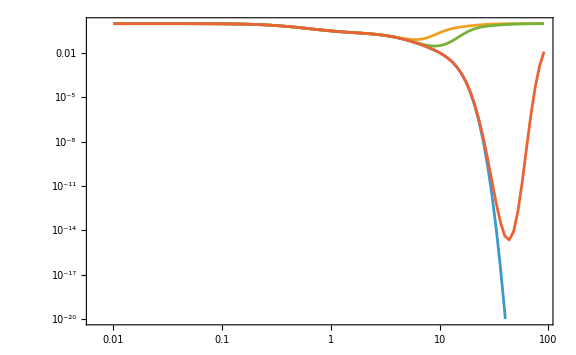

```mathematica
ListLogLogPlot[{tab,tab2,tab3,tab4},
Frame->True,
ImageSize->Large,
PlotRange->{10^-20,0},
Joined->True]
```

```mathematica
τ[300*PeV,0.15]
```

1.67887

```mathematica
τ[30*PeV,0.15,0.03Mpl]
```

0.

```mathematica
me^2/(E0 (1+z))+(E0(1+z))^2/(4elv)/.{z->0.15,E0->300TeV,elv->0.03Mpl}
```

1.30165×10^-17

```mathematica
emax
```

5.74924×10^-18

```mathematica
E0/TeV/.NSolve[me^2/(E0 (1+z))+(E0(1+z))^2/(4elv)==emax /.{z->0.15,elv->0.03Mpl},E0]
```

{-199.383,199.377,0.00632768}

```mathematica
MyTao1[E0_,z0_]:=(σT c)/H0 NIntegrate[dldz[z]func2[ϵ,z] 3/4(me^2/(E0(1+z)ϵ))^2 P[√(1-me^2/(E0(1+z)ϵ))],{z,0,z0},{ϵ,Min[Max[emin,me^2/(E0 (1+z))],emax],emax}]//Quiet;
```

```mathematica
MyTao1[10TeV,0.15]
```

4.53724

```mathematica
τ[10TeV,0.15]
```

4.53724

```mathematica
term1
```

1/(8 (-1+βmax^2))3 A^2 (2 (βmax+βmax^3)-Log[1-βmax]^2+Log[1+βmax]^2+(1+βmax^4+Log[4]+βmax^2 Log[1/4 (1-βmax^2)]) Log[-1+2/(1+βmax)]+2 (-1+βmax^2) PolyLog[2,(1-βmax)/2]-2 (-1+βmax^2) PolyLog[2,(1+βmax)/2])

```mathematica
term1/.βmax->√(1-A)/.A->Me^2/(ϵ E0(1+z))
```

-1/(8 E0 (1+z) ϵ)3 Me^2 (2 (√(1-Me^2/(E0 (1+z) ϵ))+(1-Me^2/(E0 (1+z) ϵ))^(3/2))-Log[1-√(1-Me^2/(E0 (1+z) ϵ))]^2+Log[1+√(1-Me^2/(E0 (1+z) ϵ))]^2+Log[-1+2/(1+√(1-Me^2/(E0 (1+z) ϵ)))] (1+(1-Me^2/(E0 (1+z) ϵ))^2+Log[4]+(1-Me^2/(E0 (1+z) ϵ)) Log[Me^2/(4 E0 (1+z) ϵ)])-(2 Me^2 PolyLog[2,1/2 (1-√(1-Me^2/(E0 (1+z) ϵ)))])/(E0 (1+z) ϵ)+(2 Me^2 PolyLog[2,1/2 (1+√(1-Me^2/(E0 (1+z) ϵ)))])/(E0 (1+z) ϵ))

```mathematica
MyTao2[E0_,z0_]:=(σT c)/H0 NIntegrate[dldz[z]func2[ϵ,z](-1/(8 E0 (1+z) ϵ)3 Me^2 (2 (√(1-Me^2/(E0 (1+z) ϵ))+(1-Me^2/(E0 (1+z) ϵ))^(3/2))-Log[1-√(1-Me^2/(E0 (1+z) ϵ))]^2+Log[1+√(1-Me^2/(E0 (1+z) ϵ))]^2+Log[-1+2/(1+√(1-Me^2/(E0 (1+z) ϵ)))] (1+(1-Me^2/(E0 (1+z) ϵ))^2+Log[4]+(1-Me^2/(E0 (1+z) ϵ)) Log[Me^2/(4 E0 (1+z) ϵ)])-(2 Me^2 PolyLog[2,1/2 (1-√(1-Me^2/(E0 (1+z) ϵ)))])/(E0 (1+z) ϵ)+(2 Me^2 PolyLog[2,1/2 (1+√(1-Me^2/(E0 (1+z) ϵ)))])/(E0 (1+z) ϵ))/.Me->me),{z,0,z0},{ϵ,Min[Max[emin,me^2/(E0 (1+z))],emax],emax}]//Quiet;
```

```mathematica
MyTao2[10TeV,0.15]
```

4.53724

```mathematica
term2
```

-3/16 A B (7 βmax-βmax^3+Log[1-βmax]^2-Log[1+βmax]^2+1/2 (-7+2 βmax^2+βmax^4+Log[16]) (-Log[1-βmax]+Log[1+βmax])+2 PolyLog[2,(1-βmax)/2]-2 PolyLog[2,(1+βmax)/2])

```mathematica
IntPart[ϵ_,E0_,z_,elv_,n_:1,s_:1,Me_:me]:=Module[{A,B,βmax,t1,t2},
A=Me^2/(ϵ E0 (1+z));
B=-s((E0(1+z))/elv)^n(E0 (1+z))/(2ϵ);
βmax=√(1-(2A)/(2+B));
t1=1/(8 (-1+βmax^2))3 A^2 (2 (βmax+βmax^3)-Log[1-βmax]^2+Log[1+βmax]^2+(1+βmax^4+Log[4]+βmax^2 Log[1/4 (1-βmax^2)]) Log[-1+2/(1+βmax)]+2 (-1+βmax^2) PolyLog[2,(1-βmax)/2]-2 (-1+βmax^2) PolyLog[2,(1+βmax)/2]);
Echo[t1];
t2=-3/16 A B (7 βmax-βmax^3+Log[1-βmax]^2-Log[1+βmax]^2+1/2 (-7+2 βmax^2+βmax^4+Log[16]) (-Log[1-βmax]+Log[1+βmax])+2 PolyLog[2,(1-βmax)/2]-2 PolyLog[2,(1+βmax)/2]);
Echo[t2];
t1+t2
]
```

```mathematica
Clear[MyTao];
MyTao[E0_,z0_,elv_,n_:1,s_:1,Me_:me]:=(σT c)/H0 NIntegrate[dldz[z]func2[ϵ,z] IntPart[ϵ,E0,z,elv,n,s,Me],{z,0,z0},{ϵ,Min[Max[emin,me^2/(E0 (1+z))+s((E0(1+z))/elv)^n(E0(1+z))/4],emax],emax}]//Quiet;
```

```mathematica
IntPart[ϵ,E0,z,elv,n,1,Me]/.{z->0.15,ϵ->1 eV,E0->10TeV,elv->0.03 Mpl,n->1,s->1,Me->me}
```

0.050661

```mathematica
IntPart[1 eV,10TeV,0.15,0.03 Mpl,1,1,me]
```

0.050661

```mathematica
IntPart[1eV,10TeV,0.15,0.03Mpl]
```

0.050661

0.0138958

0.0645568

```mathematica
MyTao[10TeV,0.15,Mpl]
```

3.97722

```mathematica
10TeV
```

1.60218×10^-6

```mathematica
MyTao[10TeV,0.15,Mpl,1,0]
```

4.53724

```mathematica
func2[0.1eV,0.15]
```

5.19445×10^23

```mathematica
pars={0.01,0.1,1,10,100};
```

```mathematica
data=Table[ParallelMap[{#,Exp[-MyTao[#*TeV,0.15, x*Mpl]]}&,PowerRange[10^-2,300,10.^(4/100)]],
{x,pars}];
```

```mathematica
noLV=ParallelMap[{#,Exp[-MyTao[#*TeV,0.15, Mpl,1,0]]}&,PowerRange[10^-2,300,10.^(4/100)]];
```

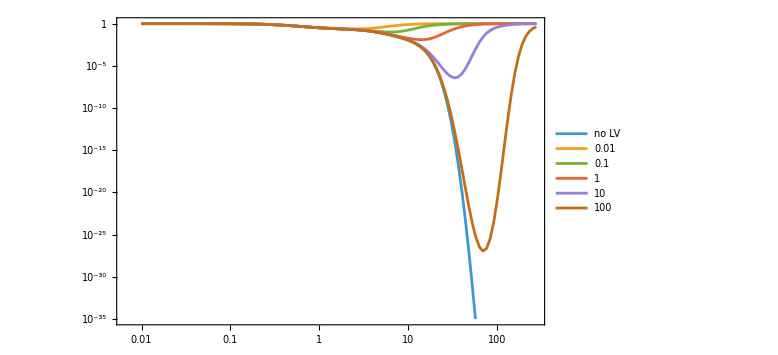

```mathematica
ListLogLogPlot[Prepend[data,noLV],
Frame->True,
ImageSize->Large,
PlotRange->{10^-35,0},
Joined->True,
PlotLegends->Placed[LineLegend[Prepend[pars,"no LV"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Left,Bottom}],
GridLines->Automatic
]
```